```mathematica
α=2.;u0=1.*10^-8;
V[r_]=-1/r;
k:=√(2e);δe1={};δe2={};δe3={};δe4={};
```

```mathematica
r2=u0;
```

```mathematica
ii=1;
Do[
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
If[ii==1,{Print[e,"  ",1/(2I)Log[Gamma[1-I/k]/Gamma[1+I/k]]];ii++;}, ];
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
If[ii==2,{Print[e,"  ",1/(2I)Log[Gamma[1-I/k]/Gamma[1+I/k]]];ii++;}, ];
e=0.01;
sol3=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.77}];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[δe3,{Log10[r1],δ3}];
If[ii==3,{Print[e,"  ",1/(2I)Log[Gamma[1-I/k]/Gamma[1+I/k]]];ii++;}, ];
e=0.1;
sol4=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.77}];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[δe4,{Log10[r1],δ4}];
If[ii==4,{Print[e,"  ",1/(2I)Log[Gamma[1-I/k]/Gamma[1+I/k]]];ii++;}, ];
Print[r1"  ",δ1"  ",δ2"  ",δ3"  ",δ4"  "],{r1,100000.,900000.,100000.}]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

0.0001  1.27606+0. ⅈ

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

0.001  -0.778532+0. ⅈ

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

0.01  -1.25044+5.55112×10^-17 ⅈ

0.1  -0.311203+5.55112×10^-17 ⅈ

100000.   -0.14022   -0.722767   -1.24867   -0.311147

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

200000.   -0.992458   -0.750617   -1.24956   -0.311175

```mathematica
δe1
δe2
δe3
δe4
```

{{2.,-0.566616},{2.30103,1.51749},{2.47712,1.36187},{2.60206,-0.879633},{2.69897,0.913589},{2.77815,-0.188463},{2.8451,-0.896662},{2.90309,-1.51635},{2.95424,1.10115}}

{{2.,0.217106},{2.30103,-0.46131},{2.47712,-0.699464},{2.60206,-0.831793},{2.69897,-0.911824},{2.77815,-0.965828},{2.8451,-1.00568},{2.90309,-1.03652},{2.95424,-1.05985}}

{{2.,-0.256327},{2.30103,-0.28347},{2.47712,-0.292784},{2.60206,-0.29729},{2.69897,-0.300076},{2.77815,-0.301939},{2.8451,-0.303232},{2.90309,-0.304239},{2.95424,-0.305015}}

{{2.,0.295684},{2.30103,0.294803},{2.47712,0.29451},{2.60206,0.294364},{2.69897,0.294276},{2.77815,0.294217},{2.8451,0.294175},{2.90309,0.294144},{2.95424,0.294119}}

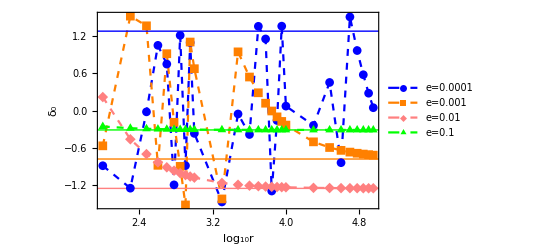

```mathematica
ListPlot[{δe1,δe2,δe3,δe4},Frame->True,FrameTicks->{{All,None},{All,None}},Joined->True,PlotMarkers->Automatic,ImageSize->Full,FrameLabel->{"log_10r","δ_0"},RotateLabel->False,PlotStyle->{{Dashed,Yellow},{Dashed,Gray},{Dashed,Pink},{Dashed,Green}},Axes->None,Epilog->{{Yellow,Thin,InfiniteLine[{0,1.2760617237454488},{1,0}],Inset[Style["δ_0(e=0.0001)=1.27606",15],{2.7,1.4}]},{Gray,Thin,InfiniteLine[{0,-0.7785323639595991},{1,0}],Inset[Style["δ_0(e=0.001)=-0.778532",15],{5.3,-0.9}]},{Pink,Thin,InfiniteLine[{0,-1.2504420054816177},{1,0}],Inset[Style["δ_0(e=0.01)=-1.25044",15],{2.4,-1.3}]},{Green,Thin,InfiniteLine[{0,-0.31120281839896935},{1,0}],Inset[Style["δ_0(e=0.1)=-0.311203",15],{5.3,-0.2}]}},PlotLegends->{"e=0.0001","e=0.001","e=0.01","e=0.1"}]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_NA_Coulomb_etest.eps",%];
```